NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

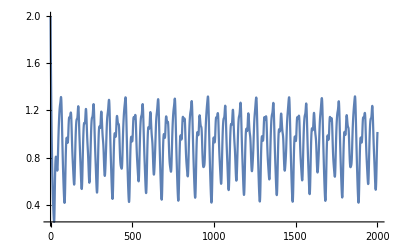

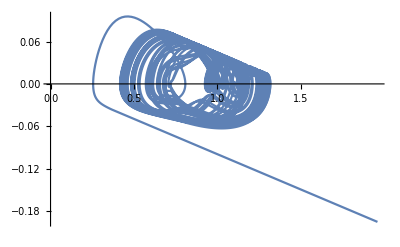

```mathematica
tau=17.0;
X=2000;
s=NDSolve[{x'[t]==(0.2*x[t-tau])/(1+x[t-tau]^10)-0.1*x[t],x[0]==2.0},x,{t,-100,X}];
SetDirectory[NotebookDirectory[]];
Export["./mgdata.txt",SetPrecision[Table[Evaluate[{t,x[t]}/.s],{t,0.0,X,0.1}][[All,1]],6],"CSV"];
Plot[Evaluate[x[t]/.s],{t,0,X},PlotRange->All]
ListPlot[Table[Evaluate[{x[t],D[x[t],t]}/.s],{t,0.0,X,0.2}][[All,1]], Joined->True]
```